# Thermodynamik-Plots

In diesem Worksheets werden die Plots der thermodynamischen Größen T_H, C, S angefertigt. Es basiert wesentlich auf Calc11/th-plots.nb. In Calc11 wurden die Rechnungen auch das letzte mal gemacht.

## 0. Definitionen

```mathematica
ClearAll[h, z0]
(* Holographisches Modell in n Dimensionen *)
h[z_,n_] := 1/(1 + (1/z)^(2+n))
(* z0 = r0 / L: Extremal Radius *)
z0[n_] := 1/(1+n)^(1/(2+n));

(* hα-Modell in n Dimensionen *)
hAlpha[z_,n_,α_] := 1/(1 + (1/z)^α / 2)^((3+n)/α)
α0[n_] := (3+n)/Log[2+n] Log[(3+n)/2]
hα0[z_,n_] := hAlpha[z,n,α0[n]]
(* Extremal Radius fuer hα-Modell *)
z0α[n_,α_] := 1/(1+n)^(1/α)
z0α0[n_] := z0α[n,α0[n]]
```

### “Generic” thermodynamic functions

Die Hawking-Temperatur hat die Einheit 1/L. Also ist Tz=T*L dimensionslos.
Parameter von Tz:
* H = Modell (h oder hAlpha)
* zH = Temp an Radius zH
* n = Dimension

```mathematica
ClearAll[Tz]
Tz[H_, zH_, n_] :=1/(4 Pi zH)(1+n-zH(D[H[zz,n],zz]/.{zz-> zH})/H[zH,n])
```

Die Wärmekapazität wird über die Ableitung der Masse und Ableitung der Hawking-Temp errechnet.
Die Masse wird wie in der Masterarbeit definiert verwendet, bloß dass hier (L^(n+1))_* bereits in z eingebaut ist.
Die physikalische Dimension von [C]=[M]/[r] * [r]/[T] = [M]/[T] = [M] [L] = 1. Hier ist also keine Skalierung nötig.

Da Tz=T*L und M=Mz*MStar, ist CC~=Mz/Tz MStar*L. Und MStar=1/L.

```mathematica
Ω[d_] := (2 Pi^((d+1)/2))/Gamma[(d+1)/2]
Mz[H_,zH_,n_] :=(n+2)/2 Ω[n+2]/(8Pi) zH^(n+1)/H[zH,n] (* M=Mz*MStar *)
(* Heat capacity als CC[] weil C[] in Mathematica reserviert ist *)
(* Ableiten nach neuer Variable falls zH ein Komposit ist (zB zH=z*z0[n]) *)
CC[H_,zH_,n_] := D[Mz[H,xH,n],xH]/D[Tz[H,xH,n],xH]/.{xH-> zH} // FullSimplify
```

```mathematica
(* Heat Capacity der Schwarzschild-Tangherlini-Metrik *)
CCSTM[zH_,n_] := CC[1&,zH,n]
```

```mathematica
(* Entropie, hier einfach eingegeben, eine Effektivfunktion fuer Holo. *)
Sh[zH_,n_] = 4π (zH^(n+2)-1)+4π (n+2) Log[zH];
SSTM[zH_,n_] = 4π(zH^(n+2));
```

### Hilfsfunktionen zum Plotten

```mathematica
(* Vorbereitungen fuer den Export *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
(* Labels direkt auf Funktionen anzeigen *)
ClearAll[EpiLabels]
EpiLabels[xpoint_,data_, labels_, axisratio_:1]:= (* labels and data must have same dimension *)
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Text[
Rotate[labels⟦n⟧,ArcTan[ data'[xpoints⟦n⟧]⟦n⟧ / axisratio](*, {Left,Bottom} *)],
{xpoints⟦n⟧, 0 + data[xpoints⟦n⟧]⟦n⟧},
Background -> White
(* Opacity[0.8,White]*)
] ~Table~{n, Range@Length@labels}]
(* Maximum finden (im typischen Bereich fuer Subscript[T, H]. Function muss genau ein Argument haben.) *)
maximum[function_] :=FindMaximum[{function[z],1≤z≤3},{z,2}] /. { ({y_,{_-> xval_}}) -> {xval,y}}
(* Function von Listen zu einer Liste von Funktionen... *)
maxima[functions_] := maximum@Function[z,#]&/@ functions[z]
(* aus remnant-plot.nb *)
point[color_, xcoord_,extend_:0.07] := Inset[
Graphics@{Opacity[0.9], color, Disk[]},
(* {x,y}, {xOrig,yOrig}, scaling --> see Inset doku *)
{xcoord, 0}, {0,0},extend
]
(* Some generic colors *)
{coldColor,hotColor} = {RGBColor[0.24720000000000014,0.24,0.6], Darker@Red};
```

## Hawking-Temp T_H

### Vorbereitungen für den Plot

```mathematica
holoN={0,1,3,4};
holoColors = {Darker@Yellow, Darker@Green, Red, Blue};
holoTemps[z_] = Tz[h,z *z0[#],#] &/@ holoN; (* must be function for EpiLabels *)
STGTemps= (1+#)/(4 Pi z*z0[#]) & /@ holoN;
holoTCompareFuncs = Join[holoTemps[z], STGTemps]
holoTLabels = "n="<>ToString@# &/@holoN
(* Critical temperatures finden *)
HoloTMaxima = maxima@holoTemps
```

{(1-2/((1+1/z^2) z^2))/(4 π z),(2-6/((1+2/z^3) z^3))/(2 2^(2/3) π z),(4-20/((1+4/z^5) z^5))/(2 2^(3/5) π z),(5^(1/6) (5-30/((1+5/z^6) z^6)))/(4 π z),1/(4 π z),1/(2^(2/3) π z),2^(2/5)/(π z),(5 5^(1/6))/(4 π z)}

{n=0,n=1,n=3,n=4}

{{2.05816,0.0238958},{2.01998,0.0701929},{1.85863,0.182821},{1.78324,0.244657}}

### Temperaturplot für Holography

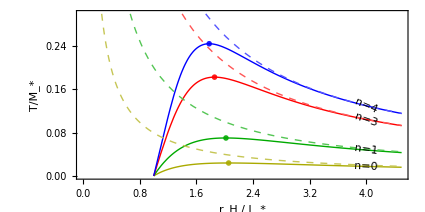

```mathematica
fig=Plot[Evaluate@holoTCompareFuncs,
{z,0,4.5},
PlotRange-> {0,0.3},
PlotStyle-> holoColors~Join~({Dashed,Lighter@#}&/@holoColors),
PlotRangePadding -> None,
FrameLabel -> {"r_H / L_*", "T/M_*"},
Frame-> True,
Epilog-> Join[
{EpiLabels[4, holoTemps, holoTLabels, 0.3/4]},
Inset[
Graphics@{Opacity[0.9], #⟦2⟧, Disk[]},
(* {x,y}, {xOrig,yOrig}, scaling --> see Inset doku *)
#⟦1⟧, {0,0}, 0.07
]& /@ Transpose@{HoloTMaxima,holoColors}
],
AspectRatio -> 0.5,
ImageSize-> 15 cm
]
```

```mathematica
Export["../figures/temperature-plot-holography-n.pdf", Show@fig]
```

../figures/temperature-plot-holography-n.pdf

### Temperaturvergleich Holo Halpha

```mathematica
hαTemps[z_] = Tz[hα0,z *z0α0[#],#] &/@ holoN;
hhCompareTemps = Join[hαTemps[z],holoTemps[z]];
HαTMaxima =maxima@hαTemps
```

{{1.96935,0.0243932},{1.92741,0.0738335},{1.81396,0.191304},{1.7573,0.254375}}

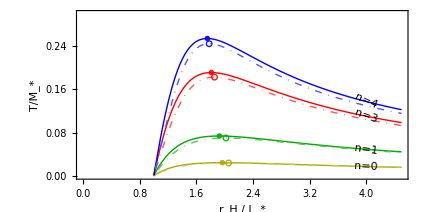

```mathematica
fig=Plot[Evaluate@hhCompareTemps,
{z,0,4.5},
PlotRange-> {0,0.3},
PlotStyle-> holoColors~Join~({DotDashed,Lighter@#}&/@holoColors),
PlotRangePadding -> None,
FrameLabel -> {"r_H / L_*", "T/M_*"},
Frame-> True,
Epilog-> Join[{EpiLabels[4, hαTemps, holoTLabels, 0.3/4]},
Inset[
Graphics@{Opacity[0.9], #⟦2⟧, Disk[]},
(* {x,y}, {xOrig,yOrig}, scaling --> see Inset doku *)
#⟦1⟧, {0,0}, 0.07
]& /@ Transpose@{HαTMaxima,holoColors},
Inset[
Graphics@{Opacity[0.9], #⟦2⟧, Circle[]},
(* {x,y}, {xOrig,yOrig}, scaling --> see Inset doku *)
#⟦1⟧, {0,0}, 0.07
]& /@ Transpose@{HoloTMaxima,holoColors}
],
AspectRatio -> 0.5,
ImageSize-> 15 cm
]
```

```mathematica
Export["../figures/temperature-plot-halpha-n.pdf", Show@fig]
```

../figures/temperature-plot-halpha-n.pdf

## Heat Capacity

### Heat Capacity-Plot für Holography

```mathematica
CCs = {0-> Darker@Magenta, 2-> Darker@Green, 3-> Red, 4-> Blue, 5 -> Darker@Yellow};
{CCNs,holoCCColors}=Transpose[CCs/.{Rule-> List}];
(* Rechne Subscript[r, C] nochmal unabhängig aus. Könnte einfach Ergebnisse HoloTMaxima recyclen,
   dann muesste aber die Auswahl der N's identisch sein, also holoN == CCNs. *)
HoloCritical[n_] := First@maximum@Function[z,Tz[h,z z0[n],n]]
(* Zum Testen ausgeben: Die Werte Subscript[r, C] *)
HoloCritical /@ (Range@Length@CCNs-1)
```

{2.05816,2.01998,1.94159,1.85863,1.78324}

```mathematica
HoloCCLabels = "n="<>ToString@#&/@CCNs
HoloCCs[zH_] = CC[h,(zH+HoloCritical[n]) z0[n] ,n]~Table~ {n,CCNs};
STMCCs = CCSTM[(zH+HoloCritical[n]) z0[n] , n]~Table~ {n,CCNs};
HoloCCCompareFuncs = Join[HoloCCs[zH], STMCCs]
```

{n=0,n=2,n=3,n=4,n=5}

{-(6.28319 (3.23603+zH (4.11633+zH)) (5.23603+zH (4.11633+zH))^2)/(-0.000156916+zH (18.4085+zH (21.4162+zH (8.23265+zH)))),-(8.77298 (13.2111+zH (29.2773+zH (22.6186+zH (7.76635+zH)))) (17.2111+zH (29.2773+zH (22.6186+zH (7.76635+zH))))^2)/(0.0000990392+zH (422.244+zH (1183.37+zH (1436.43+zH (980.778+zH (409.882+zH (105.553+zH (15.5327+zH)))))))),-(9.68946 (21.1804+zH (59.6685+zH (64.2069+zH (34.5452+zH (9.29317+zH))))) (26.1804+zH (59.6685+zH (64.2069+zH (34.5452+zH (9.29317+zH)))))^2)/(0.00125659+zH (1334.24+zH (4996.05+zH (8434.72+zH (8452.85+zH (5567.46+zH (2506.08+zH (770.483+zH (155.453+zH (18.5863+zH)))))))))),-(9.92201 (31.1558+zH (108.193+zH (151.681+zH (113.412+zH (47.6992+zH (10.6994+zH)))))) (37.1558+zH (108.193+zH (151.681+zH (113.412+zH (47.6992+zH (10.6994+zH))))))^2)/(0.00907889+zH (3495.89+zH (16606.8+zH (36486.2+zH (49089.2+zH (45072.1+zH (29679.9+zH (14281.5+zH (5005.47+zH (1247.53+zH (209.876+zH (21.3989+zH)))))))))))),-(9.47033 (43.1353+zH (179.852+zH (314.099+zH (304.751+zH (177.409+zH (61.9667+zH (12.0245+zH))))))) (50.1353+zH (179.852+zH (314.099+zH (304.751+zH (177.409+zH (61.9667+zH (12.0245+zH)))))))^2)/(-0.0297968+zH (7962.13+zH (46251.9+zH (126474.+zH (216132.+zH (258002.+zH (227143.+zH (151428.+zH (77156.4+zH (29944.1+zH (8715.89+zH (1845.06+zH (268.522+zH (24.049+zH)))))))))))))),-6.28319 (2.05816+zH)^2,-8.77298 (1.94159+zH)^4,-9.68946 (1.85863+zH)^5,-9.92201 (1.78324+zH)^6,-9.47033 (1.71779+zH)^7}

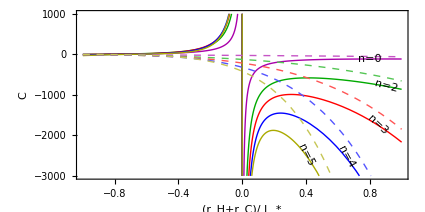

```mathematica
fig=Plot[
Evaluate@HoloCCCompareFuncs,
{zH,-1,1},
PlotRange-> {-3000,1000},
PlotStyle-> holoCCColors~Join~({Dashed,Lighter@#}&/@holoCCColors),
PlotRangePadding -> None,
FrameLabel -> {"(r_H+r_C)/ L_*", "C"},
Frame-> True,
Epilog->{
EpiLabels[{0.8,0.9,0.85,0.65,0.4}, HoloCCs, HoloCCLabels, 4000/1.5]
},
AspectRatio -> 0.5,
ImageSize-> 15 cm
]
```

```mathematica
Export["../figures/heat-capacity-plot-holography-n.pdf", Show@fig]
```

../figures/heat-capacity-plot-holography-n.pdf

### Naiver Heat-Capacity-Plot (auf expliziten Wunsch von PN)

```mathematica
HoloCCsNaive[zH_] = CC[h,zH * z0[n] ,n]~Table~ {n,CCNs};
STMCCsNaive = CCSTM[zH*z0[n] , n]~Table~ {n,CCNs};
HoloCCCompareFuncsNaive = Join[HoloCCsNaive[zH], STMCCsNaive];
```

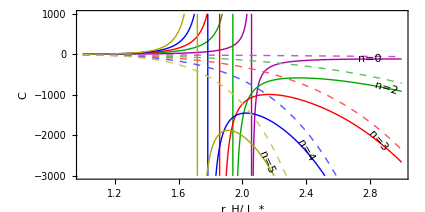

```mathematica
fig=Plot[
Evaluate@HoloCCCompareFuncsNaive,
{zH,1,3},
PlotRange-> {-3000,1000},
PlotStyle-> holoCCColors~Join~({Dashed,Lighter@#}&/@holoCCColors),
PlotRangePadding -> None, PlotRangeClipping->False,
FrameLabel -> {"r_H/ L_*", "C"},
Frame-> True,
Epilog->{
EpiLabels[{2.8,2.9,2.85,2.4,2.15}, HoloCCsNaive, HoloCCLabels, 4000/1.5],
(*point[fancyBlueColor, 1, 0.05]*)
},
AspectRatio -> 0.5,
ImageSize-> 15 cm
]
```

```mathematica
Export["../figures/heat-capacity-plot-naive-holography-n.pdf", Show@fig]
```

../figures/heat-capacity-plot-naive-holography-n.pdf

### Vergleich Heat-Capacity Holography mit Hα

```mathematica
Hα0Critical[n_] := First@maximum@Function[z,Tz[hα0,z z0α0[n],n]]
(* Zum Testen ausgeben: Die Werte Subscript[r, C] *)
Hα0Critical /@ (Range@Length@CCNs-1)
Hα0CCs[zH_] = CC[hα0,(zH+Hα0Critical[n]) z0α0[n] ,n]~Table~ {n,CCNs};
HoloHαCCCompares = Join[Hα0CCs[zH],HoloCCs[zH]];
```

{1.96935,1.92741,1.87263,1.81396,1.7573}

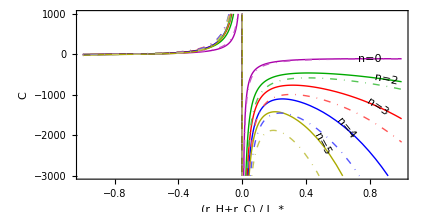

```mathematica
fig=Plot[
Evaluate@HoloHαCCCompares,
{zH,-1,1},
PlotRange-> {-3000,1000},
PlotStyle-> holoCCColors~Join~({DotDashed,Lighter@#}&/@holoCCColors),
PlotRangePadding -> None,
FrameLabel -> {"(r_H+r_C) / L_*", "C"},
Frame-> True,
Epilog->{
EpiLabels[{0.8,0.9,0.85,0.65,0.5}, Hα0CCs, HoloCCLabels, 4000/1.5]
},
AspectRatio -> 0.5,
ImageSize-> 15 cm
]
```

```mathematica
Export["../figures/heat-capacity-plot-halpha-n.pdf", Show@fig]
```

../figures/heat-capacity-plot-halpha-n.pdf

## Big Picture: Temperature, Heat Capacity und Entropie im Vergleich

Während alle Plots hier obendrüber in Calc11 im Prinzip bereits gemacht wurden (wenngleich viel weniger instruktiv, da zu viele Dimensionen geplottet und nicht die richtigen Vergleiche gemacht), ist der folgende Plot neu.
Er zeigt die Temperatur und Heat Capacity direkt übereinander, um so die verschiedenen Phasen des BHs zu illustrieren. Gearbeitet wird am Holography-BH.

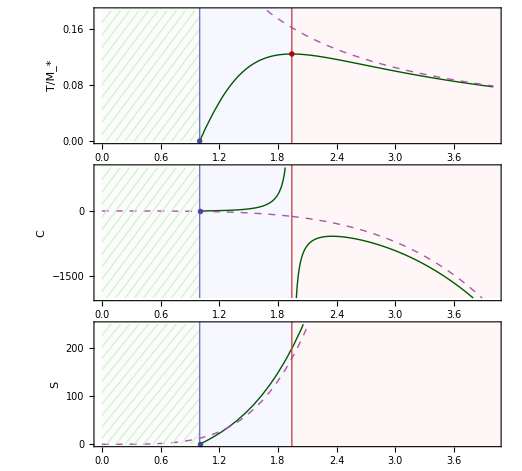

```mathematica
n = 2;
zRange = {0,4};
aspectRatio = 0.3;
imageSize = 18cm;
(* 4/3^(3/4) = dummer Faktor... ist halt alles nicht genau hier *)
g00h[z_] =1-4/3^(3/4)h[z z0[n],n]/(z z0[n])^(1+n);
g00SSM[z_] = 1-  4/3^(3/4)/(z z0[n])^(1+n);
rC=maximum@Function[z,Tz[h,z *z0[n],n]]; (* Coordinate tuple *)
colors = {Darker[Green,0.65],{Dashed,Lighter@Purple}};

(* shorthands: *)
auto = Automatic; hidden = Directive[FontOpacity->0,FontSize->0];
simpleRect[xmin_,xmax_,color_,ymin_:-2000,ymax_:2000] := {EdgeForm[],Lighter[color,0.95],Rectangle[{xmin,ymin},{xmax, ymax}]}
simpleLine[xpos_,color_,ymin_:-2000,ymax_:2000] := {Lighter[color,0.3],Line@{{xpos,ymin},{xpos,ymax}}}
simpleDot[pos_, color_] :=Inset[Graphics@{Opacity[0.9], color, Disk[]},pos, {0,0}, 0.07]

(* Nonaccessible range shading *)
shading[ymin_:0,ymax_:50]:= RegionPlot[r < 1-0.001, {r,0,3},{y,ymin,ymax},
Mesh->20,MeshFunctions->{#1-#2/(ymax-ymin)&},MeshShading->{None},
BoundaryStyle->None,MeshStyle-> GrayLevel[0.9]];

(* Area shading and separation, Prolog for each graph *)
areas[ymin_:-2000,ymax_:2000] := {
simpleRect[0,1,Lighter@Green, ymin, ymax],
simpleRect[1,First@rC, Lighter@Blue, ymin, ymax],
simpleRect[First@rC,5, Lighter@Red, ymin, ymax]
};
lines[ymin_:-2000,ymax_:2000] := {
simpleLine[1, coldColor, ymin, ymax],
simpleLine[First@rC, hotColor, ymin, ymax]
};
(* g00 in diesem Zusammenhang ist FALSCH, da es auf der r-Achse nicht den Horizont, sondern den Radius aufträgt.
g00 passt hier einfach nicht dazu. *)
fg00 = Plot[Evaluate@{g00h[z],g00SSM[z]},{z, First@zRange, Last@zRange},
PlotRangePadding -> None, PlotRangeClipping -> False, PlotRange-> {0,1(*1.5 g00h[1]*)}, PlotStyle-> colors,
Frame-> True, FrameLabel -> {Null, "g_00"},
(* Diese Codezeile sorgt fuer einen buggy PDF-Export *)
(* FrameTicksStyle-> {{auto,auto}, {hidden,auto }},*)
FrameTicks-> {{auto,auto},{auto,{{1,"r_0"}, {First@rC, "r_C"}}}},
AspectRatio -> aspectRatio, ImageSize-> imageSize,
(* ImagePadding: {{left,right},{bottom,top}} *)
ImagePadding -> {{59,1},{5,40}},
Prolog-> areas[0,1],
Epilog -> {simpleDot[{1,g00h[1]},Red]}
];
fT = Plot[Evaluate@{
 Tz[h,z *z0[n],n],
(1+n)/(4 Pi z*z0[n])
},{z,First@zRange, Last@zRange},PlotRange-> {0,1.5}Last@rC,
PlotRangePadding -> None,PlotRangeClipping-> True, PlotStyle-> colors,
Frame-> True, FrameLabel -> {Null, "T/M_*"},
AspectRatio -> aspectRatio, ImageSize-> imageSize,
(*FrameTicksStyle-> {auto, hidden},*)
FrameTicks-> {{auto,auto},{auto,{{1,"r_0"}, {First@rC, "r_C"}}}},
ImagePadding -> {{59,1},{5,40}}, (*{45/2,45/2} *)
Prolog-> areas[], Epilog-> lines[]~Join~{
simpleDot[{1, 0}, coldColor],
simpleDot[rC, hotColor],
}
]~Show~shading[0,1.5 Last@rC];
fC = Plot[Evaluate@{
If[zH>1,CC[h,zH z0[n] ,n],],
CCSTM[zH z0[n],n]
},{zH,First@zRange, Last@zRange}, PlotRange -> {-2000,1000},
Exclusions-> {First@rC},
PlotRangePadding -> None, PlotRangeClipping-> True,PlotStyle-> colors,
FrameLabel-> {Null, "C"},
FrameTicksStyle-> {auto, hidden},
Frame-> True,
ImagePadding -> {{59,1},{45/2,45/2}},ImageMargins-> {{0,0},{0,0}}, (* {{left,right},{bottom,top}} *)
AspectRatio -> aspectRatio,ImageSize-> imageSize,
Prolog-> areas[],Epilog-> lines[]~Join~{simpleDot[{1,0}, coldColor]}
]~Show~shading[-2000,1000];
fS = Plot[Evaluate@{
If[zH > 1, Sh[zH , n],],
SSTM[zH,n]
},
{zH,First@zRange, Last@zRange},
PlotRange->{0,250},
PlotRangePadding -> None, PlotRangeClipping-> True,PlotStyle-> colors,
FrameLabel -> {"r_H / L_*", "S"},
AspectRatio -> aspectRatio,ImageSize-> imageSize,
ImagePadding -> {{59,1},{40,5}},ImageMargins-> {{0,0},{0,0}}, (* {{left,right},{bottom,top}} *)
Prolog-> areas[],
Frame-> True,Epilog-> lines[]~Join~{simpleDot[{1,0},coldColor]}
]~Show~shading[0,250];
fig= 
Show@Graphics[
GraphicsGrid[{(*{fg00},*){fT},{fC},{fS}},Frame->None, Spacings-> 0]
]
```

```mathematica
Export["../figures/thermodynamic-big-plot.pdf", Show@fig]
```

../figures/thermodynamic-big-plot.pdf